```mathematica
Физические константы;
ae = 14959787000000;
mp=1.67262192369*10^(-24);
kb = 1.38*10^(-16);
me=9.1093837015*10^(-28);
c=2.99792458*10^(10);
λ0=121.56701 * 10^(-9) * 100;
ech=4.8032046729976595417*10^(-10);(*Заряд электрона*)
f=0.41641;
E0=1.112650056053*10^(-21);(*диэлектрическая проницаемость вакуума*)
G=6.7 * 10^(-8);(*Гравитационная постоянная*)
MasSolar=1.9885 * 10^(33);
pc=206264.8*ae;
Rsun=6.96 * 10^(10);
Lsun=3.828 * 10^(33);
(*Светимость Эрг/с*)
σe=0.345;(*0.325 чистое томсоновское сечение на свободный электрон, делённое на массу протона,с учётом состава см^2 / г*)
```

```mathematica
Параметры модели   в  СГС;
γ=5/3;
Teff=40000;(*30500 Поверхностная температура звезды*)
M=50*MasSolar;(*18.7 Масса звезды*)
L=800000*Lsun;(*91000*)
B0=1000.0;(*43*)
R0=20*Rsun;(*8.5*)
rho0=1.2*10^(-11);
α=0.65;(*CAK exponent*)
Q=2000;(*CAK force*)
Qmax=0.004*Q;(*CAK force*)
dM=2.0* (10^(-6)) * MasSolar/(365*24*60*60);  (*было 10^(-8)*)
V∞=1880*10^5;
Vrot= 400*10^5 ;
```

```mathematica
Выбор характерных значений;
RR=R0;
Rho=rho0;
VV=V∞;
TT=RR/VV;
```

```mathematica
Рассчитываем нужные величины;
Γe=σe*L/(4*π*G*M*c);
f1=-G*M/(RR^2) * TT/VV;
f2=σe*L/(4*π*RR^2*c)* TT/VV;
fCAK=((σe*Q)^(1-α)*L*VV^α/((1-α)*4*π*RR^2 * c^(α+1)*Rho^α*RR^α))* TT/VV;
p0=1.6666666*(rho0/mp)*kb*Teff;
vth=Sqrt[2*kb*Teff/mp];
eta=B0*B0*R0*R0/(V∞*dM);
abc=1+(0.25 + eta)^(1/4)-0.25^(1/4);
ArcSin[Sqrt[1/abc]]
```

0.582751

```mathematica
Печатаем нужные параметры;
Print["Сила гравитации = ", f1]
Print["Сила радиации (континум) = ", f2]
Print["Сила line-driven = ", fCAK]
Print["Безразмерная контстанта p = c * rho; c =  ", p0/(Rho*VV*VV)/(rho0/Rho)]
Print["Безразмерная тепловая скорость (она постоянна в решении) = ",vth/VV]
Print["Безразмерное магнитное поле Br = ",B0/(VV * Sqrt[Rho])]
Print["Безразмерное скорость вращения звезды = ",1.0 * Vrot/VV]
```

Сила гравитации = -0.135399

Сила радиации (континум) = 0.0570027

Сила line-driven = 0.0276084

Безразмерная контстанта p = c * rho; c =  0.000155623

Безразмерная тепловая скорость (она постоянна в решении) = 0.0136656

Безразмерное магнитное поле Br = 1.53551

Безразмерное скорость вращения звезды = 0.212766

```mathematica
Sqrt[2*kb*Teff/mp]
eta = B0*B0*R0*R0/(dM*V∞ )
```

2.56913×10^6

0.151115

```mathematica
eta = B0*B0*R0*R0/(dM*V0 );
RA=eta^(1/4) ;
Vrot= 400*10^5 ;
Omega= Vrot /R0;
a0=Sqrt[kb*Teff/mp];
Γe=σe*L/(4*π*G*M*c)
```

0.396592

```mathematica
Выбор характерных значений;
Vin= 0.7*10^5;
ρin=dM/(4 * π*Vin*R0*R0);
ρin2=dM/(4 * π*a0/5*R0*R0);
pin=1.6666666*(ρin/mp)*kb*Teff;
RR=R0;
Rho=ρin;
VV=V0 ;
TT=RR/VV;
Vorbit=Sqrt[G*M/R0];
W=Vrot/Vorbit
ρin2/Rho
Print["Граничные условия:"]
Print["Безразмерная контстанта p = c * rho; c =  ", pin/(Rho*VV*VV)/(ρin/Rho)]
Print["Безразмерная скорость в гран условиях = ",1.0*Vin/VV]
Print["Гран условия на плотность: c/V; c = ",Vin/VV]
Print["Безразмерная скорость на бесконечности = ",V0/VV]
Print["Оценка скорости на бесконечности = ",Sqrt[alpha/(1-alpha)]*Vesc/VV]
Print["Азимутальная скорость Vphi = Vrot * sin(the); б/р Vrot = ",1.0 * Vrot/VV]
Print["Радиальное магнитное поле Br = ",B0/(VV * Sqrt[Rho])]
Print["Начальные условия:"]
Print["Константа в плотности: rho = c/v(r); c = ", (dM/(4 * π))/(Rho*VV*RR*RR)]
Print["Перевести безразмерное время в часы: умножить на ", TT/60/60]
Print["Перевести безразмерный расход массы в 10^-8 Msolar/year = ", Rho*VV*RR*RR/MasSolar*(60*60*24*365)/(10^(-8))]
```

0.616386

0.220637

Граничные условия:

Безразмерная контстанта p = c * rho; c =  0.000186401

Безразмерная скорость в гран условиях = 0.000466667

Гран условия на плотность: c/V; c = 0.000466667

Безразмерная скорость на бесконечности = 1

Оценка скорости на бесконечности = (√(alpha/(1-alpha)) Vesc)/150000000

Азимутальная скорость Vphi = Vrot * sin(the); б/р Vrot = 0.266667

Радиальное магнитное поле Br = 0.0314065

Начальные условия:

Константа в плотности: rho = c/v(r); c = 0.000466667

Перевести безразмерное время в часы: умножить на 1.09556

Перевести безразмерный расход массы в 10^-8 Msolar/year = 37515.1

```mathematica
Γe=σe*L/(4*π*G*M*c);
Vesc=Sqrt[2*G*M*(1-Γe)/R0];
Vcrit=Sqrt[G*M*(1-Γe)/Req];
Omeg= Vrot /Vcrit;
Omeg2= Vrot /Sqrt[G*M*(1-Γe)/Rpole];
zeta=V0 /Vesc;
```

```mathematica
Решаем уравнение на критическое значение;
gamma=0.35;
beta=0.8;
NSolve[x==π/Sqrt[2] *zeta*(1.0 - beta)*(1-x)^ gamma,x]
```

{{x→0.538247}}

```mathematica
Omegth=0.538246768856072;
Omegd=Sqrt[1.5 *Omegth^2/(1.0 + 0.5 * Omegth^2) ];
```

```mathematica
Omeg 
Omegd
```

0.659549

0.616101

```mathematica
Ассимтотическая закрутка;
Vinf[the0_]:=1.3*zeta*Vesc*(1-Sin[the0]*Vrot/Vcrit)^gamma;
phiMax[the0_]:=1/(1-beta) * Sin[the0]*Vrot/Vinf[the0];
phiMax[15*π/180]*180/π
phiMax[30*π/180]*180/π
phiMax[45*π/180]*180/π
phiMax[60*π/180]*180/π
phiMax[75*π/180]*180/π
phiMax[85*π/180]*180/π
Vinf[90*π/180]/10^5
```

16.2392

33.7995

51.7689

68.447

80.9331

85.1386

1337.38

```mathematica
Вычисляем массовые силы;
f1=-G*M/(RR^2) * TT/VV;
f2=σe*L/(4*π*RR^2*c)* TT/VV;
f1
f2
```

-0.187168

0.0225764

```mathematica
Vrot^2 / RR* TT/VV
```

0.0711111

```mathematica
σe*Rho*VV*RR/VV
```

86.6341

```mathematica
Sqrt[2*kb*Teff/mp]/VV
```

0.014956

```mathematica
Solve[Vthe==u*Cos[phi] - v*Sin[phi]&&Vr==u*Cos[phi] + v*Sin[phi],{u,v}]
```

{{u→1/2 (Vr Sec[phi]+Vthe Sec[phi]),v→1/2 (Vr Csc[phi]-Vthe Csc[phi])}}

```mathematica
Алгоритм подбора нужных параметров;
Шаг 1;
Γe=σe*L/(4*π*G*M*c);
Vesc=Sqrt[2*G*M*(1-Γe)/R0];
ksi=(V0 /Vesc);
alpha = ksi^2 / (1 + ksi^2)
Vth=Sqrt[2*kb*Teff/mp];
AA=(4*π*M*G/(Vth*σe))*alpha*(1-alpha)^((1-alpha)/alpha) ;
BB=Γe^(1/alpha)*(1-Γe)^(-(1-alpha)/alpha);
k=(dM/(AA BB))^alpha
```

0.752342

0.18792

```mathematica
Solve[dM==AA * kk^(1/alpha)*BB,kk]
```

```mathematica
D[(1/r)^(0.4),r]
```

-0.4 (1/r)^1.4

```mathematica
aa[r_]:= 1.6666666*(1/mp)*kb*Teff*(R0/r)^(0.4);
daa[r_]:=-0.4*1.6666666*(1/mp)*kb*Teff*(R0)^(0.4) * (1/r)^1.4;
vth[r_]:=Sqrt[2*kb*Teff*(R0/r)^(0.4)/mp];
A[r_]:=-G*M*(1-Γe)/r^2+2*aa[r]/r-daa[r];
B[r_]:=(Γe*G*M*(k/(RR*r)^2)*(4*π/(σe*vth[(RR*r)]*dM))^(alpha))/(RR^(-1-alpha) * VV^(2-2*alpha));
```

```mathematica
G*M/RR^2/VV/VV*RR
```

0.187168

```mathematica
aa[r_]:= 27960.09315292678*(1/r)^(0.4);
daa[r_]:=-0.000074560248407805 * (1/r)^1.4;
vth[r_]:=0.014955960489739347*(1/r)^(0.4);
A[r_]:=-0.18716787994891446/r^2+2*aa[r]/r-daa[r];
B[r_]:=(Γe*G*M*(k/(RR*r)^2)*(4*π/(σe*vth[(RR*r)]*dM))^(alpha))/(RR^(-1-alpha) * VV^(2-2*alpha));
```

```mathematica
ClearAll[rhs];
rhs[r_?NumericQ,v_?NumericQ]:=Module[{vp},vp=vp/. FindRoot[(v-aa[r]/v)*vp==A[r]+B[r]*(r^2*v*vp)^alpha,{vp,0.1}  (*начальное приближение*)];
{1,vp}];
```

```mathematica
rhs[3,0.1]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{1,-2.97758×10^-7-2.25259×10^-9 ⅈ}

```mathematica
StreamPlot[rhs[r,v],{r,1.0001,2},{v,0.0001,1},StreamPoints->Fine,FrameLabel->{"r","v"},PlotLabel->"Phase portrait"]
```

StreamPlot[rhs[r,v],{r,1.0001,2},{v,0.0001,1},StreamPoints→Fine,FrameLabel→{r,v},PlotLabel→Phase portrait]

```mathematica
ss=NDSolve[(v[r]-aa[r]/v[r])*v'[r]==-G*M*(1-Γe)/r^2+2*aa[r]/r-daa[r]+Γe*G*M*(k/r^2)*(4*π/(σe*vth[r]*dM))^(alpha) * (r^2 * v [r]* v'[r])^(alpha)&&v[R0]==0.1*10^5,v,{r,R0,1.1*R0}];
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::ndsz: At r == 5.916×10^11, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {5.91601×10^11} lies outside the range of data in the interpolating function. Extrapolation will be used.

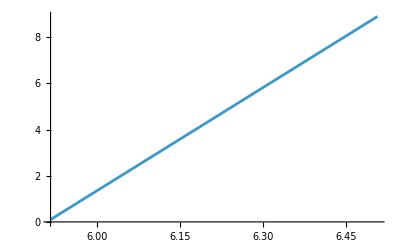

```mathematica
Plot[(v[r]/.ss)/10^5,{r,R0,1.1*R0}]
```

```mathematica
Solve[(v-aa/v)*dv==-G*M*(1-Γ)/r^2+2*aa/r-daa+Γ*G*M*(k/r^2)*(4*π/(σe*vth*dM))^(alpha) * (r^2 * v * dv)^(alpha),dv]
```

```mathematica
A=-G*M*(1-Γ)/r^2+2*aa/r-daa
B=Γ*G*M*(k/r^2)*(4*π/(σe*vth*dM))^(alpha)
```

```mathematica
Solve[(v-aa/v)*dv==A+B * (r^2 * v * dv)^(alpha),dv]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[dv (-aa/v+v)==A+B (dv r^2 v)^alpha,dv]

```mathematica
2+2
```

4

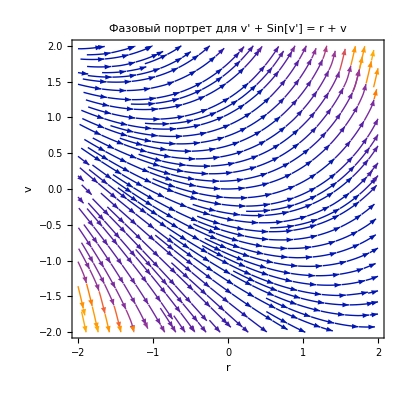

```mathematica
(*Очищаем переменные*)ClearAll[rhs];

(*Функция,возвращающая вектор поля {1,v'}*)
rhs[r_?NumericQ,v_?NumericQ]:=Module[{vp},(*Решаем неявное уравнение vp+Sin[vp]==r+v относительно vp*)vp=vp/. FindRoot[vp+Sin[vp]==r+v,{vp,0}];
{1,vp}];

(*Строим фазовый портрет*)
StreamPlot[rhs[r,v],{r,-2,2},{v,-2,2},StreamPoints->Fine,FrameLabel->{"r","v"},PlotLabel->"Фазовый портрет для v' + Sin[v'] = r + v"]
```